```mathematica
(* https://www.expii.com/solve/70/5 *)
(* Other than wave functions, there are lots of other types of functions such as exponential functions and polynomial functions. In fact,polynomial functions, while they seem pretty simple can approximate all other functions pretty well!
In fact, consider the function e^x. Let p(x) be the cubic (degree 3) polynomial that has the minimum distance from e^x, where the distance is defined as Integrate[Abs[p(x)-e^x], {x, 0, 1}]. Compute this minimum distance to the nearest thousandth. *)
```

```mathematica
Series[Exp[x],{x,a,5}]
```

ⅇ^a+ⅇ^a (x-a)+1/2 ⅇ^a (x-a)^2+1/6 ⅇ^a (x-a)^3+1/24 ⅇ^a (x-a)^4+1/120 ⅇ^a (x-a)^5+O[x-a]^6

```mathematica
p[x_,a_]:=Exp[a] (1 + (x-a) + 1/2 (x-a)^2 + 1/6 (x-a)^3);
dis[a_] :=NIntegrate[Abs[p[x,a]-Exp[x]],{x,0,1}]
```

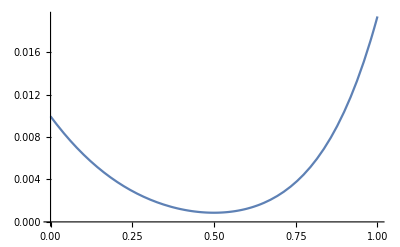

```mathematica
Plot[dis[a],{a,0,1}]
```

```mathematica
NMinimize[{dis[a],a>=0, a<=1},a]
```

{0.000863838,{a→0.5}}

```mathematica
dis[0.5]
```

0.000863838